```mathematica
f11={{1,0,0},{0,1,0},{0,0,1}};
f22={{1,0,0},{0,-1,0},{0,0,0}};
f33=1/Sqrt[3] {{1,0,0},{0,1,0},{0,0,-2}};
f12={{0,1,0},{1,0,0},{0,0,0}};
f21={{0,-I,0},{I,0,0},{0,0,0}};
f13={{0,0,1},{0,0,0},{1,0,0}};
f31={{0,0,-I},{0,0,0},{I,0,0}};
f23={{0,0,0},{0,0,1},{0,1,0}};
f32={{0,0,0},{0,0,-I},{0,I,0}};

Id=IdentityMatrix[3];

τ=π/2;

Hid=1/√2(KroneckerProduct[f12,f12,Id]+KroneckerProduct[f21,f21,Id]+KroneckerProduct[f13,f13,Id]+KroneckerProduct[f31,f31,Id]+KroneckerProduct[Id,f12,f12]+KroneckerProduct[Id,f21,f21]+KroneckerProduct[Id,f13,f13]+KroneckerProduct[Id,f31,f31]);

η0=Flatten[KroneckerProduct[{0,a,b},{1,0,0},{1,0,0}]];
η1=Flatten[KroneckerProduct[{1,0,0},{1,0,0},{0,a,b}]];
```

```mathematica
n=4;
J=Table[1/2 Sqrt[i (n-i)],{i,n-1}]
```

{(√3)/2,1,(√3)/2}

```mathematica
MatrixExp[-I f12 τ]//MatrixForm;
MatrixExp[-I f21 τ]//MatrixForm;
MatrixExp[-I f13 τ]//MatrixForm;
MatrixExp[-I f31 τ]//MatrixForm;
{0,1,0}.MatrixExp[-I f12 τ].{1,0,0};
{0,1,0}.MatrixExp[-I f21 τ].{1,0,0};
{0,0,1}.MatrixExp[-I f13 τ].{1,0,0};
{0,0,1}.MatrixExp[-I f31 τ].{1,0,0};
```

```mathematica
Exp[-I π]*η1.MatrixExp[-I Hid τ].η0//Simplify
```

a^2+b^2

```mathematica
MatrixExp[-I φ f21]//MatrixForm
MatrixExp[-I φ f31]//MatrixForm
MatrixExp[-I π/2 f22]//MatrixForm
```

(Cos[φ] | -Sin[φ] | 0
Sin[φ] | Cos[φ] | 0
0 | 0 | 1)

(Cos[φ] | 0 | -Sin[φ]
0 | 1 | 0
Sin[φ] | 0 | Cos[φ])

(-ⅈ | 0 | 0
0 | ⅈ | 0
0 | 0 | 1)

{1/3,((-3-3 ⅈ)+√(24+18 ⅈ))/(6 (1+(-1)^(1/3))),(-1/6-ⅈ/6) ((2+ⅈ)+√3)}

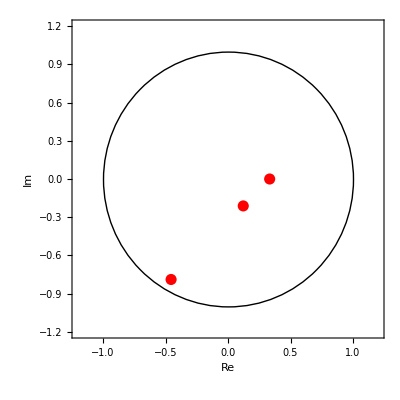

```mathematica
ω=Exp[(2 π I)/3];
Ω={{1,1,1},{1,ω,ω^2},{1,ω^2,ω}};
W=LinearSolve[Ω,{-I,I,1}];
FullSimplify[W]
complexSplit=Function[z,{Re@z,Im@z},Listable];
ComplexPlot[list_,d_]:=ListPlot[complexSplit@list,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->(Directive[#,PointSize[.02]]&/@{Purple,Darker@Green,Orange,Cyan,Magenta,Blue,Red}),Epilog->{Circle[{0,0},1],Circle[{1/#,1/#},Sqrt[2]/#]&/@Table[i,{i,2,d}]}]
ComplexPlot[W,0]
```